## Plot: Initial Values

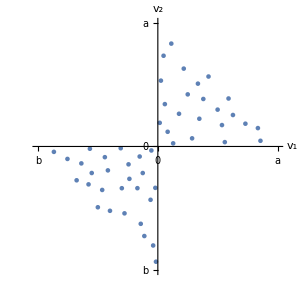

```mathematica
removeClosest[s_]:=Block[{n,c},(n=Nearest[s];
c=SortBy[Table[{i,Norm[s[[i]]-n[s[[i]],2][[2]]]},{i,1,Length[s]}],(#[[2]])&][[1,1]];
Delete[s,c])];
removeClosest[s_]:=s/;Length[s]<2;

(* Creating list of initial Values *)
rangev0=Range[-1,1,0.1];
r=Random[];
listv0=Select[RandomReal[{-2,2},{1000,2}],(Sign[#[[1]]*#[[2]]]≥0 && Abs[#[[1]]+#[[2]]]≤2)&];
listv0=Nest[removeClosest,listv0,Length[listv0]-50];


fontsize=25;

g0=ListPlot[listv0,AspectRatio->Automatic, AxesLabel->{Style["v_1",FontSize->fontsize,FontFamily->Times,Italic],Style["v_2",FontSize->fontsize,FontFamily->Times,Italic]},
Ticks->{{{2,Style["a",FontSize->fontsize-5,FontFamily->Times,Italic]},0,{-2,Style["b",FontSize->fontsize-5,FontFamily->Times,Italic]}},{{2,Style["a",FontSize->fontsize-5,FontFamily->Times,Italic]},0,{-2,Style["b",FontSize->fontsize-5,FontFamily->Times,Italic]}}},
PlotRange->{{2,-2},{2,-2}},
ImageSize->300]
```

```mathematica
figsDirectory=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"figs"}];

Export[FileNameJoin[{figsDirectory,"initial-values.pdf"}],g0]
```

D:\MastersMathematica\Matematica\MathematicaOpticalFlow\CyclopeanOpticalFlow\Figures\figs\initial-values.pdf